## Standard voter model

```mathematica
dxdt = (1-x-zP-zM)*(x+zP)-x(1-x-zP) // FullSimplify
```

zP-(x+zP) (zM+zP)

```mathematica
(*No zealots*)
dxdt /. {zM-> 0, zP-> 0} // FullSimplify
```

0

```mathematica
(*Balanced zealots*)
dxdtBalanced = dxdt /. {zM-> z/2, zP-> z/2} // FullSimplify
Solve[dxdtBalanced == 0, x]
D[dxdtBalanced, x]
```

-1/2 z (-1+2 x+z)

{{x→(1-z)/2}}

-z

```mathematica
(*Absorbing zealots*)
dxdtAbsorbing = dxdt /. {zM->0, zP-> z} // FullSimplify
Solve[dxdtAbsorbing== 0, x]
D[dxdtAbsorbing, x]
```

-z (-1+x+z)

{{x→1-z}}

-z

```mathematica
(*Unbalanced zealots*)
dxdtUnbalanced = dxdt /. {zM->(1-δ)/2*z, zP-> (1+δ)/2*z} // FullSimplify
Solve[dxdtUnbalanced == 0, x]
D[dxdtUnbalanced, x]
```

-1/2 z (2 x+(-1+z) (1+δ))

{{x→-1/2 (-1+z) (1+δ)}}

-z

## q-voter model

### Balanced zealots

```mathematica
(*Standard q=1 voter model*)
dxdt = (1-x-z)*(x+z/2)^q-x(1-x-z/2)^q
Solve[(dxdt/. {q-> 1}) == 0, x]
```

-x (1-x-z/2)^q+(1-x-z) (x+z/2)^q

{{x→(1-z)/2}}

```mathematica
(*Define funciton*)
B[x_, q_, z_] := Log[(2*x+z)/(2*(1-x)-z)]-1/q*Log[x/(1-x-z)] // FullSimplify
```

```mathematica
(*Limits of f(x,q,z)*)
Assuming[q>0, Limit[B[x,q,z], x-> 0]]
Assuming[q>0, Limit[B[x,q,z], x-> 1-z]]
```

∞

-∞

```mathematica
(*Find stationary points of f(x,q,z)*)
df[x_, q_, z_] := D[B[x,q,z], x] // FullSimplify
sol = Solve[df[x,q,z] == 0, x];
x1 = sol[[1]][[1]][[2]]  // FullSimplify
x2 = sol[[2]][[1]][[2]] // FullSimplify
```

1/2 (1-z-(√((1+q (-1+z)) (-1+z) (-1+q+z)))/(-1+q+z))

1/2 (1-z+(√((1+q (-1+z)) (-1+z) (-1+q+z)))/(-1+q+z))

```mathematica
(*Solutions are always real*)
Assuming[{0<z<1, q>0},FullSimplify[Reduce[(1+q (-1+z)) (-1+z) (-1+q+z)>0, z] ]]
```

q+z<1||1+q z<q

```mathematica
(*Solutions only bounded provided q > 1*)
(*Not we have altered the form to account for the assumption that they are real*)
Assuming[{0<z<1 && (q+z<1||1+q z<q)},FullSimplify[Reduce[0<x1<1-z, z, Reals]]]
Assuming[{0<z<1 && (q+z<1||1+q z<q)},FullSimplify[Reduce[0<x2<1-z, z, Reals]]]
```

q>1

q>1

```mathematica
(*The function is the same after reflecting in both x=(1-z)/2 and y=0*)
-B[1-z-x,q,z] // FullSimplify
B[x,q,z]
```

Log[-(-1+x+z)/x]/q-Log[-1+2/(2 x+z)]

-Log[-x/(-1+x+z)]/q+Log[-1-2/(-2+2 x+z)]

```mathematica
(*Show the equivilance of the numerical solution and the critical zealotry formula*)
NSolve[(B[x1, q, z] /. {q-> 1.1}) == 0, z][[1]][[1]][[2]]
zC[q_]:= 1-1/q
zC[1.1]

(*Can also substiute in our solution, any q should evaluate to essentially 0*)
B[x1, q, z] /. z->1-1/q /. q-> 1.4
```

0.0909091

0.0909091

0.

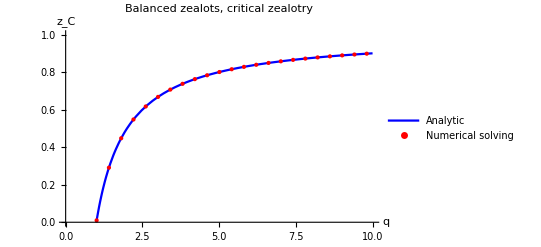

```mathematica
(*The zero of this function gives the zC*)
B[x1, q, z]// FullSimplify;

(*Define the first function*)
zCana1[q_]:=1-1/q;

(*Define the second function's equation*)
zCnum[q_,z_]:=Log[(-1+q+z-√((1+q (-1+z)) (-1+z) (-1+q+z)))/(-1+q+z+√((1+q (-1+z)) (-1+z) (-1+q+z)))]-Log[(2+2 q (-1+z)-2 z+z^2+2 √((1+q (-1+z)) (-1+z) (-1+q+z)))/((-2+z) z)]/q==0

(*Solve for z at discrete points using FindRoot*)
discretePoints=Table[{q,z/. FindRoot[zCnum[q,z],{z,0.25}]},{q,1.01,10,0.4}];

(*Plot both functions on the same plot*)
Show[
Plot[
zCana1[q],
{q,1,10},
PlotRange->{{0, 10}, {0, 1}},
AxesLabel->{"q","z_C"},
PlotLabel->"Balanced zealots, critical zealotry",
PlotStyle->{Blue},
PlotLegends->{"Analytic"}
],

ListPlot[
discretePoints,
PlotStyle->{Red,PointSize[Large]},
PlotLegends->{"Numerical solving"}
]
]
```

```mathematica
(*Solve for the fixed points numerically*)
eq = (1-x-z)*(x+z/2)^q-x*(1-x-z/2)^q;
Solve[(eq/.{q-> 1.5, z-> 0.1}) == 0, x]
```

{{x→0.0169873},{x→0.45},{x→0.883013}}

```mathematica
(*write roots to file for bifurcation diagram*)
roots[z_]:=(1-x-z)*(x+z/2)^q-x*(1-x-z/2)^q /. q->1.5

(*Define the range of z values*)
zValues=N[Subdivide[0,1,5000]];

(*Initialize empty lists to store the results for each root*)
root1Results={};
root2Results={};
root3Results={};

(*Solve the equation for each value of z and store the real roots*)
Do[

(*Solve the equation for x when roots[z]==0*)
solutions=Solve[roots[z]==0,x];

(*Extract the x-values from the solutions*)

realRoots=Select[x/. solutions,NumericQ[#]&&Im[#]==0&];
(*Sort the roots to maintain order (if required)*)
realRoots=Sort[realRoots];

(*Assign roots to respective lists*)
If[Length[realRoots]≥1,AppendTo[root1Results,{z,realRoots[[1]]}]];
If[Length[realRoots]≥2,AppendTo[root2Results,{z,realRoots[[2]]}]];
If[Length[realRoots]≥3,AppendTo[root3Results,{z,realRoots[[3]]}]];

,{z,zValues}
];

(*Define the file paths for the output files*)
filePath1="D:\\Users\\CKitc\\GitHub\\PhD-Zealots\\data\\qvm\\balanced\\qvm_balanced_x1.txt";
filePath2="D:\\Users\\CKitc\\GitHub\\PhD-Zealots\\data\\qvm\\balanced\\qvm_balanced_x2.txt";
filePath3="D:\\Users\\CKitc\\GitHub\\PhD-Zealots\\data\\qvm\\balanced\\qvm_balanced_x3.txt";

(*Write the results to three different files*)
Export[filePath1,root1Results,"Table"];
Export[filePath2,root2Results,"Table"];
Export[filePath3,root3Results,"Table"];
```

### Absorbing zealots

```mathematica
(*Standard q=1 voter model*)
dxdt = (1-x-z)*(x+z)^q-x(1-x-z)^q
Solve[(dxdt/. {q-> 1}) == 0, x]
```

-x (1-x-z)^q+(1-x-z) (x+z)^q

{{x→1-z}}

```mathematica
(*Define funciton*)
f[x_, q_, z_] := Log[(x+z)/(1-(x+z))]-1/q*Log[x/(1-x-z)] // FullSimplify
```

```mathematica
(*Limits of f(x,q,z)*)
Assuming[q>0, Limit[f[x,q,z], x-> 0]]
Assuming[q>0, Limit[f[x,q,z], x-> 1-z]]
```

∞

DirectedInfinity[-1+q]

```mathematica
(*Find stationary points of f(x,q,z)*)
df[x_, q_, z_] := D[f[x,q,z], x] // FullSimplify
sol = Solve[df[x,q,z] == 0, x];
x1 = sol[[1]][[1]][[2]] // FullSimplify
```

-((-1+z) z)/(-1+q+z)

```mathematica
Assuming[q>0 && 0<z<1, FullSimplify[Reduce[0<x1 < 1-z, q]]]
```

q>1

```mathematica
(*Small check*)
Z = 0.8;
1-Z
NSolve[(f[x,q,z]/. {q-> 0.9, z-> Z})== 0, x]
NSolve[(f[x,q,z]/. {q-> 0.9, z-> Z})== 0, x][[1]][[1]][[2]] - (1-Z)
```

0.2

{{x→0.2}}

-1.024×10^-7

```mathematica
(*Determine where this stationary point is valid*)
Assuming[q>0 && 0<z<1, FullSimplify[Reduce[0<x1<1-z]]]
```

q>1

```mathematica
(*Can numerically determine the critical zealotry*)
Solve[(f[x1, q, z]/. q-> 2) == 0, z] // N
Solve[(Log[q*z/((1-q)*(z-1))]-1/q*Log[z/(q-1)]== 0) /. q-> 2, z]
```

{{z→0.171573}}

{{z→3-2 √2}}

```mathematica
(*Can get a good analaytical approximation with Newton-Raphson in 2 iterations*)
1-Exp[f[x1, q , z]]// FullSimplify
eq[z_, q_] := 1+(q (z/(-1+q))^((-1+q)/q))/(-1+z);
Newton[z_, q_] := z - eq[z, q]/(D[eq[x, q], x] /. x-> z);

n = 1-1/q;
z0 =((1-n)/(1+n))^(1/n);
z1 = Newton[z0, q]  // FullSimplify;
z2 = Newton[z1, q] // Simplify;

z1 /. q-> 1.5// N
z2 /. q-> 1.5 // N
```

1+(q (z/(-1+q))^((-1+q)/q))/(-1+z)

0.105571

0.105892

```mathematica
1+(q (z/(-1+q))^((-1+q)/q))/(-1+z) /. q-> 1/(1-x) // FullSimplify
```

-(-1+x+z-x z+((-1+1/x) z)^x)/((-1+x) (-1+z))

```mathematica
(*zC has a series solution, where n=1-1/q*)
seriesSolution[n_] := 1/n*Sum[(-1)^k/Factorial[k]*(n/((1-n)^(1-1/n)))^(k+1)*Gamma[(k+1)/n]/(Gamma[(k+1)/n-k+1]),{k,0,150}];
ana[q_] := seriesSolution[1-1/q] // N;

(*And a good approx*)
approx[q_] := (q-1)*(2*q-1)^((q-1/3)/(1-q));
```

```mathematica
(*Write in the full q dependence form*)
ana[q_]:=q/(q-1)*NSum[(-1)^k/Factorial[k]*((q-1)/(q^(q/(q-1))))^(k+1)*Gamma[q*(k+1)/(q-1)]/(Gamma[q*(k+1)/(q-1)-k+1]),{k,0,∞}]

q = 1.1
N[ana[q]]
```

1.1

ComplexInfinity

General::munfl: (2.08127×10^-238)/710998587804863451854045647463724949736497978881168458687447040000000000000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.40758×10^-242 (-1))/40526919504877216755680601905432322134980384796226602145184481280000000000000 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (9.51963×10^-247)/2350561331282878571829474910515074683828862318181142924420699914240000000000000 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

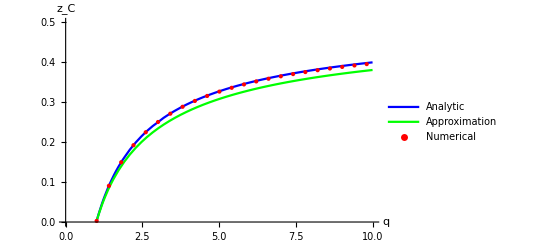

C://Users/Christopher/Documents/GitHub/PhD-Zealots/figures/q_voter_zealots/absorbing_zealots_critical_z.png

```mathematica
(*Define the second function's equation*)
zCnum[q_,z_]:=1+(q*(z/(-1+q))^((-1+q)/q))/(-1+z)==0

(*Solve for z at discrete points using FindRoot*)
discretePoints=Table[{q,z/. FindRoot[zCnum[q,z],{z,0.25}]},{q,1.01,10,0.4}];

(*Plot both functions on the same plot*)
plot = Show[
Plot[
ana[q],
{q,1,10},
PlotRange->{{0, 10}, {0, 0.5}},
AxesLabel->{"q","z_C"},
PlotStyle->{Blue},
PlotLegends->{"Analytic"}
],
Plot[
approx[q],
{q,1,10},
PlotRange->{{0, 10}, {0, 0.5}},
PlotStyle->{Green},
PlotLegends->{"Approximation"}
],
ListPlot[
discretePoints,
PlotStyle->{Red,PointSize[Large]},
PlotLegends->{"Numerical"}
]
]

Export["C://Users/Christopher/Documents/GitHub/PhD-Zealots/figures/q_voter_zealots/absorbing_zealots_critical_z.png", plot]
```

```mathematica
(*Write the numerical solution*)
trinomial[q_,z_]:=Module[{n=1-1/q},(1-n)^(n-1)/n^n*z^n+z-1];
qValues=N[Subdivide[1.3,10,20]];

zNumerical=
Quiet@ParallelTable[
{q,N[FindRoot[trinomial[q,z],{z,0.25}][[1]][[2]]]},
{q,qValues}];

filePath="/home_th/kitching/Documents/PhD/PhD-Zealots/data/nonlinear_vm/absorbing/qvm_absorbing_zC_numerical.txt";
Export[filePath,zNumerical,"Table"];
```

```mathematica
(*Write the analytical solution*)
qValues=N[Subdivide[1.1,10,100]];

zResults=
Quiet@ParallelTable[
{q,N[ana[q]]},
{q,qValues}
];

filePath="/home_th/kitching/Documents/PhD/PhD-Zealots/data/nonlinear_vm/absorbing/qvm_absorbing_zC_analytic.txt";
Export[filePath,zResults,"Table"];
```

```mathematica
(*write roots to file for bifurcation diagram*)
roots[z_]:=(1-x-z)*(x+z)^q-x*(1-x-z)^q /. q->0.5

(*Define the range of z values*)
zValues=N[Subdivide[0,1,5000]];

(*Initialize empty lists to store the results for each root*)
root1Results={};
root2Results={};
root3Results={};

(*Solve the equation for each value of z and store the real roots*)
Do[

(*Solve the equation for x when roots[z]==0*)
solutions=Solve[roots[z]==0,x];

(*Extract the x-values from the solutions*)
realRoots=Select[x/. solutions,NumericQ[#]&&Im[#]==0&];

(*Sort the roots to maintain order (if required)*)
realRoots=Sort[realRoots];

(*Assign roots to respective lists*)
If[Length[realRoots]≥1,AppendTo[root1Results,{z,realRoots[[1]]}]];
If[Length[realRoots]≥2,AppendTo[root2Results,{z,realRoots[[2]]}]];
If[Length[realRoots]≥3,AppendTo[root3Results,{z,realRoots[[3]]}]];

,{z,zValues}
];

(*Define the file paths for the output files*)
filePath1="D:/Users/CKitc/GitHub/PhD-Zealots/data/nonlinear_vm/absorbing/q_0.5/qvm_absorbing_x1.txt";
filePath2="D:/Users/CKitc/GitHub/PhD-Zealots/data/nonlinear_vm/absorbing/q_0.5/qvm_absorbing_x2.txt";
filePath3="D:/Users/CKitc/GitHub/PhD-Zealots/data/nonlinear_vm/absorbing/q_0.5/qvm_absorbing_x3.txt";

(*Write the results to three different files*)
Export[filePath1,root1Results,"Table"];
Export[filePath2,root2Results,"Table"];
Export[filePath3,root3Results,"Table"];
```

```mathematica
Quiet[ana[1.5]]
```

0.10596

```mathematica
(*Find stable interior root for use in finite populations*)
roots[z_]:=(1-x-z)*(x+z)^q-x*(1-x-z)^q /. q-> 3
Solve[roots[0.24] == 0, x]
```

{{x→0.0457143},{x→0.135},{x→0.76}}

```mathematica
(*Find stable interior point for quasi-distribution*)
(*define the function whose roots we want*)
f[z_,x_]:=(1-x-z)*(x+z)^q-x*(1-x-z)^q /. q-> 0.8;

(*generate list of {z,minRoot}*)
results=Reap[
Do[
(*find all real solutions in x for this z*)
sols=x/. NSolve[f[z,x]==0,x,WorkingPrecision->20];
realSols=Select[sols,Im[#]==0&]//Chop;
If[Length[realSols]==2,
(*compute your normalized root*)
minNorm=Min[realSols]/(1-z-0.01);
(*only keep if≤1*)
If[minNorm<=1,
Sow[{z,minNorm}]
]
],
{z,0.01,0.98,0.01}
]
][[2,1]];

(*write to disk as a two-column whitespace-delimited file*)
Export["D:\\Users\\CKitc\\GitHub\\PhD-Zealots\\data\\nonlinear_vm\\quasi_stationary_distribution\\q=0.8\\deterministic_fixed_point_pos.txt",results,"Table"];
```

NSolve::precw: The precision of the argument function ({-(0.99-x)^0.8 x+(0.99-x) (0.01+x)^0.8}) is less than WorkingPrecision (20).

NSolve::precw: The precision of the argument function ({-(0.98-x)^0.8 x+(0.98-x) (0.02+x)^0.8}) is less than WorkingPrecision (20).

NSolve::precw: The precision of the argument function ({-(0.97-x)^0.8 x+(0.97-x) (0.03+x)^0.8}) is less than WorkingPrecision (20).

General::stop: Further output of NSolve::precw will be suppressed during this calculation.

### Unbalanced zealots

```mathematica
(*Standard q=1 voter model*)
dxdt = (1-x-z)*(x+1/2(1+δ)z)^q-x(1-x-1/2(1+δ)z)^q
Solve[(dxdt/. {q-> 1}) == 0, x] // FullSimplify
```

-x (1-x-1/2 z (1+δ))^q+(1-x-z) (x+1/2 z (1+δ))^q

{{x→-1/2 (-1+z) (1+δ)}}

```mathematica
(*Define funciton*)
U[x_, q_, z_, δ_] := Log[(2*x+(1+δ)*z)/(2*(1-x)-(1+δ)*z)]-1/q*Log[x/(1-x-z)] // FullSimplify
```

```mathematica
(*Limits of U(x,q,z,δ)*)
Assuming[q>0, Limit[U[x,q,z, δ], x-> 0]]
Assuming[q>0, Limit[U[x,q,z, δ], x-> 1-z]]
```

∞

-∞

```mathematica
(*Find stationary points of f(x,q,z)*)
df[x_, q_, z_, δ_] := D[U[x,q,z, δ], x] // FullSimplify
sol = Solve[df[x,q,z, δ] == 0, x];
x1 = sol[[1]][[1]][[2]] // FullSimplify
x2 = sol[[2]][[1]][[2]] // FullSimplify
```

(-1+q-q z+z (2+δ-z (1+δ))-√((-1+z) (-1+z+q (2+q (-1+z)+z (-2+z-z δ^2)))))/(2 (-1+q+z))

(-1+q-q z+z (2+δ-z (1+δ))+√((-1+z) (-1+z+q (2+q (-1+z)+z (-2+z-z δ^2)))))/(2 (-1+q+z))

```mathematica
(*Solutions only real under the following conditions*)
Assuming[{0<z<1, q>0, -1<δ<1},FullSimplify[Reduce[(-1+z) (-1+z+q (2+q (-1+z)+z (-2+z-z δ^2)))<0, z] ]]
```

q==1||√((1+q)^2-4 q δ^2) Abs[-1+q]<1+q (-2+q+2 z-2 z δ^2)

```mathematica
(*Solve for the z value which gives 2 stationary points*)
zC= (Solve[√((1+q)^2-4 q δ^2) Abs[-1+q]== 1+q (-2+q+2 z-2 z δ^2), z] // FullSimplify)[[1]][[1]][[2]]
zC /. {q-> 1.28, δ->-0.6}
```

((-1+q)^2-√((1+q)^2-4 q δ^2) Abs[-1+q])/(2 q (-1+δ^2))

0.265187

```mathematica
(*Solutions only bounded provided q > 1*)
(*This takes a while to run*)
Assuming[{0<z<1&& √((1+q)^2-4 q δ^2) Abs[-1+q]>1+q (-2+q+2 z-2 z δ^2) && -1<δ<1},FullSimplify[Reduce[0<x1<1-z, z]]]
Assuming[{0<z<1 && √((1+q)^2-4 q δ^2) Abs[-1+q]>1+q (-2+q+2 z-2 z δ^2) && -1<δ<1},  FullSimplify[Reduce[0<x2<1-z, z]]]
```

q>1

q>1

```mathematica
(*Evaluate U at the stationary points*)
UAtLowerStationaryPoint =Assuming[0<z<1&& √((1+q)^2-4 q δ^2) Abs[-1+q]>1+q (-2+q+2 z-2 z δ^2) && -1<δ<1 && q>1,Simplify[U[x1,q,z,δ]]];
UAtUpperStationaryPoint = Assuming[0<z<1&& √((1+q)^2-4 q δ^2) Abs[-1+q]>1+q (-2+q+2 z-2 z δ^2) && -1<δ<1 &&q>1,Simplify[U[x2,q,z,δ]]];
```

```mathematica
(*U evaluated at the upper stationary point is always > 0*)
Assuming[0<z<1&& √((1+q)^2-4 q δ^2) Abs[-1+q]>1+q (-2+q+2 z-2 z δ^2) && 0<δ<1 &&q>1,Reduce[UAtUpperStationaryPoint>0]]
```

$Aborted

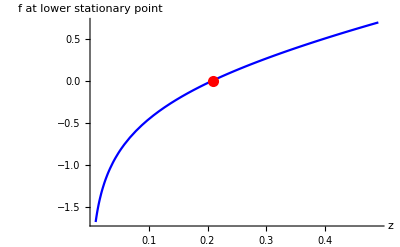

```mathematica
(*Plot root of lower stat point*)
params = {q-> 2, δ-> 0.7};
f = UAtLowerStationaryPoint /. params;
guess = zC/2 /. params;
Plot[
f,
{z,0.01,0.49},
AxesLabel->{"z","f at lower stationary point"},
PlotStyle->{Blue},
Epilog->{Red,PointSize[0.02],Point[{FindRoot[f, {z, guess}][[1]][[2]],0}]}]
```

```mathematica
(*Print U(x1)*)
UAtLowerStationaryPoint
```

1/q(Log[z (2+z (-1+δ))]-Log[(2 q (-1+z)+z (-2+z-z δ^2)+2 (1+√((-1+z) (-1+z+q (2+q (-1+z)+z (-2+z-z δ^2))))))/(-1+δ)]-q Log[-(q z (-1+δ) (-2+z+z δ))/(q (-2+z (2+z (-1+δ^2)))+2 (1-z+√((-1+z) (-1+z+q (2+q (-1+z)+z (-2+z-z δ^2))))))])

```mathematica
(*Define functions for solving for zC*)
func[z_,q_,δ_]:=1/q(Log[z (2+z (-1+δ))]-Log[(2 q (-1+z)+z (-2+z-z δ^2)+2 (1+√((-1+z) (-1+z+q (2+q (-1+z)+z (-2+z-z δ^2))))))/(-1+δ)]-q Log[-(q z (-1+δ) (-2+z+z δ))/(q (-2+z (2+z (-1+δ^2)))+2 (1-z+√((-1+z) (-1+z+q (2+q (-1+z)+z (-2+z-z δ^2))))))])
guessFunc[q_, δ_] := (((-1+q)^2-√((1+q)^2-4 q δ^2) Abs[-1+q])/(2 q (-1+δ^2)))/2;
rootFunc[q_, δ_] := FindRoot[func[z, q, δ], {z, guessFunc[q, δ]}][[1]][[2]]
```

```mathematica
(*test by solving for zC*)
rootFunc[10, 0.5]
```

0.538684

```mathematica
(*Define the range of z values*)
qValues=N[Subdivide[1.01,10,50]];
δVal=-0.9;

(*Initialize empty lists to store the results for each root*)
Results={};

(*Evaluate critical z for each q*)
rootsData=Table[
Module[
{r1},

(*Evaluate critical z*)
r1=Quiet[rootFunc[q,δVal]];
AppendTo[Results,{q,Re[r1]}];
],
{q,qValues}
];

(*Define the file paths for the output files*)
filePath="/home_th/kitching/Documents/PhD/PhD-Zealots/data/qvm/unbalanced/qvm_unbalanced_zC_delta_4.txt";

(*Write the results to three different files*)
Export[filePath,Results,"Table"];
```

## Evolutionary Games

```mathematica
πPlus = α*(x+zP)+(1-α)*(s-x+zM);
πMinus =(1-α)*(x+zP)+α*(s-x+zM);

s = 1-zM-zP;
dxdt=(s-x)*(x+zP)*πPlus - x*(s-x+zM)*πMinus// FullSimplify
```

-x (-1+x+zP) (-x-zP-α+2 (x+zP) α)-(x+zP) (-1+x+zM+zP) (1-x-zP-α+2 (x+zP) α)

### α=1/2 case

```mathematica
dxdtEdge = dxdt /. α-> 1/2 // FullSimplify
```

zP-(x+zP) (zM+zP)

```mathematica
(*No zealots*)
dxdtNo = dxdtEdge /. {zM-> 0, zP-> 0}
```

0

```mathematica
(*Balanced zealots*)
dxdtBalanced = dxdtEdge /. {zM-> z/2, zP-> z/2} // FullSimplify
Solve[dxdtBalanced == 0 , x]
D[dxdtBalanced, x]
```

-1/2 z (-1+2 x+z)

{{x→(1-z)/2}}

-z

```mathematica
(*Absorbing zealots*)
dxdtAbsorbing = dxdtEdge /. {zM-> 0, zP-> z} // FullSimplify
Solve[dxdtAbsorbing == 0 , x]
D[dxdtAbsorbing, x]
```

-z (-1+x+z)

{{x→1-z}}

-z

```mathematica
(*Unbalanced zealots*)
dxdtUnbalanced = dxdtEdge /. {zM-> (1-δ)/2*z, zP-> (1+δ)/2*z} // FullSimplify
Solve[dxdtUnbalanced == 0 , x]
D[dxdtUnbalanced, x]
```

-1/2 z (2 x+(-1+z) (1+δ))

{{x→-1/2 (-1+z) (1+δ)}}

-z

### No zealots

```mathematica
dxdt = dxdt /. {zP-> 0, zM-> 0} // FullSimplify
ϕ /. {zP-> 0, zM-> 0} // FullSimplify

(*Fixed points*)
Solve[dxdt == 0, x]

(*Evaluate gradient at the centre FP*)
D[dxdt, x] /. x-> 1/2
```

-((-1+x) x (-1+2 x) (-1+2 α))/(α+2 (-1+x) x (-1+2 α))

α+2 (-1+x) x (-1+2 α)

{{x→0},{x→1/2},{x→1}}

(-1+2 α)/(2 (1/2 (1-2 α)+α))

### Balanced zealots

```mathematica
(*Rate Eqn*)
dxdtBZ = dxdt /. {zP-> z/2, zM-> z/2}
ϕ /. {zP-> z/2, zM-> z/2} // FullSimplify

(*FPs*)
FPs = Assuming[0≤α≤1 && 0<z<1 && 0≤x≤1-z, Solve[dxdtBZ == 0, x]] // FullSimplify;
FPs[[1]][[1]][[2]]
FPs[[2]][[1]][[2]]
FPs[[3]][[1]][[2]]
```

((-1+x+z/2) (x+z/2) (-1+2 x+z)-(-1+2 x+z) (2 x^2+1/2 (-1+z) z+x (-2+2 z)) α)/(-2 (-1+x+z/2) (x+z/2)+(-1+2 x+z)^2 α)

-1/2 (-2+2 x+z) (2 x+z)+(-1+2 x+z)^2 α

ConditionalExpression[(1-z)/2, (1/(-2+2 z)+α≠0&&z<1/2)||z>1/2]

ConditionalExpression[1/2 (1-z-√(1+(2 z α)/(1-2 α))), 2 z<1&&z+2 (-1+z)^2 α>1]

ConditionalExpression[1/2 (1-z+√(1+(2 z α)/(1-2 α))), 2 z<1&&z+2 (-1+z)^2 α>1]

```mathematica
(*Critical zealotry*)
Solve[z+2(1-z)^2α == 1, z] // FullSimplify
```

{{z→1},{z→1-1/(2 α)}}

### Absorbing zealots

```mathematica
(*Rate equation*)
dxdtAZ = dxdt /. {zM-> 0, zP-> z} // FullSimplify
```

-((-1+x+z) (x-2 x^2+z-3 x z-z^2+(2 x+z) (-1+2 x+2 z) α))

```mathematica
(*FPs*)
Assuming[0<α<1 && 0<z<1 && 0≤x≤1-z, FullSimplify[Solve[dxdtAZ == 0, x]]]
```

```mathematica
{{x->ConditionalExpression[1-z, ]},{x->ConditionalExpression[1/4 (1-3 z-√((-1+z)^2+(4 z)/(1-2 α))), (1+z)^2<2 (-1+z)^2 α]},{x->ConditionalExpression[1/4 (1-3 z+√((-1+z)^2+(4 z)/(1-2 α))), (z+2 α<1+z α&&2 √2+z≠3)||(1+z)^2<2 (-1+z)^2 α]}}
```

```mathematica
(*If α>1/2, the two internal fixed points exist, when z<zC as solved for below*)
Assuming[0<α<1 && 0<z<1, FullSimplify[Solve[(1+z)^2== 2 (-1+z)^2 α, z] ]]
```

{{z→ConditionalExpression[(1-2 √2 √α+2 α)/(-1+2 α), α>1/2]}}

```mathematica
(*When α<1/2, the positive internal fixed point exists provided z<zC as solved for below*)
Assuming[0<α<1 && 0<z<1,FullSimplify[Solve[1/4 (1-3 z+√((-1+z)^2+(4 z)/(1-2 α))) == 1-z, z]]]
```

{{z→ConditionalExpression[2+1/(-1+α), α<1/2]}}

### Unbalanced Zealots

```mathematica
(*Rate equation*)
dxdtUZ = dxdt /. {zP-> (1+δ)/2*z, zM-> (1-δ)/2*z} // FullSimplify
ϕ /. {zP-> (1+δ)/2*z, zM-> (1-δ)/2*z} // FullSimplify
```

((-1+2 x+z) (-2+2 x+z+z δ) (2 x+z+z δ)-2 α (-1+2 x+z+z δ) (4 x^2+(-1+z) z (1+δ)+2 x (-2+z (2+δ))))/(4 (α (-1+2 x+z+z δ)^2-1/2 (-2+2 x+z+z δ) (2 x+z+z δ)))

1/2 (2 α+x^2 (-4+8 α)+z (-1+2 α) (1+δ) (-2+z+z δ)+4 x (-1+2 α) (-1+z+z δ))

```mathematica
(*FPs*)
Assuming[0<=α<1/2 && 0<z<1 && 0≤x≤1-z && -1<δ<1, Simplify[Solve[dxdtUZ == 0, x]]]
```

{{x→Root[-2 z+3 z^2-z^3+2 z α-4 z^2 α+2 z^3 α-2 z δ+4 z^2 δ-2 z^3 δ+2 z α δ-6 z^2 α δ+4 z^3 α δ+z^2 δ^2-z^3 δ^2-2 z^2 α δ^2+2 z^3 α δ^2+(-4+12 z-6 z^2+8 α-20 z α+12 z^2 α+8 z δ-8 z^2 δ-16 z α δ+16 z^2 α δ-2 z^2 δ^2+4 z^2 α δ^2) #1+(12-12 z-24 α+24 z α-8 z δ+16 z α δ) #1^2+(-8+16 α) #1^3&,2]}}

```mathematica
(*FPs*)
Assuming[1/2<α<= 1 && 0<z<1 && 0≤x≤1-z && -1<δ<1, Simplify[Solve[dxdtUZ == 0, x]]]
```

{{x→ConditionalExpression[Root[-2 z+3 z^2-z^3+2 z α-4 z^2 α+2 z^3 α-2 z δ+4 z^2 δ-2 z^3 δ+2 z α δ-6 z^2 α δ+4 z^3 α δ+z^2 δ^2-z^3 δ^2-2 z^2 α δ^2+2 z^3 α δ^2+(-4+12 z-6 z^2+8 α-20 z α+12 z^2 α+8 z δ-8 z^2 δ-16 z α δ+16 z^2 α δ-2 z^2 δ^2+4 z^2 α δ^2) #1+(12-12 z-24 α+24 z α-8 z δ+16 z α δ) #1^2+(-8+16 α) #1^3&,1], ]},{x→ConditionalExpression[Root[-2 z+3 z^2-z^3+2 z α-4 z^2 α+2 z^3 α-2 z δ+4 z^2 δ-2 z^3 δ+2 z α δ-6 z^2 α δ+4 z^3 α δ+z^2 δ^2-z^3 δ^2-2 z^2 α δ^2+2 z^3 α δ^2+(-4+12 z-6 z^2+8 α-20 z α+12 z^2 α+8 z δ-8 z^2 δ-16 z α δ+16 z^2 α δ-2 z^2 δ^2+4 z^2 α δ^2) #1+(12-12 z-24 α+24 z α-8 z δ+16 z α δ) #1^2+(-8+16 α) #1^3&,2], ]},{x→ConditionalExpression[Root[-2 z+3 z^2-z^3+2 z α-4 z^2 α+2 z^3 α-2 z δ+4 z^2 δ-2 z^3 δ+2 z α δ-6 z^2 α δ+4 z^3 α δ+z^2 δ^2-z^3 δ^2-2 z^2 α δ^2+2 z^3 α δ^2+(-4+12 z-6 z^2+8 α-20 z α+12 z^2 α+8 z δ-8 z^2 δ-16 z α δ+16 z^2 α δ-2 z^2 δ^2+4 z^2 α δ^2) #1+(12-12 z-24 α+24 z α-8 z δ+16 z α δ) #1^2+(-8+16 α) #1^3&,3], ]}}

```mathematica
(*Define new function who's roots are the fixed points*)
U=  Assuming[0≤α≤1 && 0<z<1 && 0<δ<1, FullSimplify[ (s-x)*(x+zP)/( x*(s-x+zM)) - πMinus/πPlus /. {zP-> (1+δ)/2*z, zM-> (1-δ)/2*z}]];

(*Expand at small x, 1/x term has +ve coefficient for all parameter values, thus U->+∞ as x->0 from above*)
firstTerm = Coefficient[Series[U,{x,0,1}], x, -1] // FullSimplify
Assuming[0≤α≤1 && 0<z<1 && 0<δ<1, FullSimplify[Reduce[firstTerm > 0]]]

(*Limit as x-> 1-z is always < 0*)
lim=Assuming[0≤α≤1 && 0<z<1 && 0<δ<1, FullSimplify[Limit[U, x-> 1-z]]]
Assuming[0≤α≤1 && 0<z<1 && 0<δ<1, FullSimplify[Reduce[lim < 0]]]
```

((-1+z) z (1+δ))/(-2+z+z δ)

True

1-2/(2 α+z (-1+2 α) (-1+δ))

True

```mathematica
(*Determining the stationary points of U amounts to solving a 4th order polynomial in x*)
eq = Assuming[0≤α≤1 && 0<z<1 && 0<δ<1 && 0≤ x ≤ 1-z, FullSimplify[D[U, x]]];
eq=Expand[Numerator[Together[eq]]];
eq=Collect[eq,x] // FullSimplify
```

-16 x^4 (-1+2 α) (-1+z (-1+2 α))-8 x (-1+z) z (1+δ) (2-3 α+z (-1+2 α) (1+δ)) (2-2 α+z (-1+2 α) (1+δ))-(-1+z) z (1+δ) (-2+z+z δ) (2-2 α+z (-1+2 α) (1+δ))^2-32 x^3 (-1+2 α) (1+z+z^2 (-1+2 α) (1+δ)-z α (2+δ))-8 x^2 (2-4 α+z (5+3 δ+3 z^2 (1-2 α)^2 (1+δ)^2+2 α (-8+7 α+6 (-1+α) δ)-z (-1+2 α) (1+δ) (-9-2 δ+α (13+5 δ))))

```mathematica
(*Stationary points of U when 1/2<α≤1*)
statPoints = Assuming[1/2<α≤ 1 && 0<z<1 && 0<δ<1 && 0≤ x ≤ 1-z, Simplify[Solve[eq == 0, x]]];
```

```mathematica
(*Extract stationary points*)
x1 = statPoints[[1]][[1]][[2]];
x2 =  statPoints[[2]][[1]][[2]];

(*Numerically solve for the z value which puts the stationary point on the x-axis*)
NSolve[(U /. x-> x1 /. {δ-> 0.7, α-> 0.7}) == 0, z]
NSolve[(U /. x-> x2 /. {δ-> 0.7, α-> 0.7}) == 0, z]
```

{{z→-2.71181×10^7},{z→0.103583}}

{}

```mathematica
(*Calculate zC for all α in range*)
delta = 0.8;
results=Table[
Module[
{sol1,sol2,nonZeroZ},

(*Solve for z*)
sol1=Quiet[NSolve[(U/. x->x1/. {δ->delta,α->alpha})==0,z]];
sol2=Quiet[NSolve[(U/. x->x2/. {δ->delta,α->alpha})==0,z]];

(*Extract non-zero solutions for z*)nonZeroZ=Select[Flatten[{z/. sol1,z/. sol2}],#>0.0001&];

(*Return {alpha,non-zero z values}*)
Table[{alpha,zVal},{zVal,nonZeroZ}]
],
{alpha,Subdivide[0.501, 0.9999, 10]}
];

(*Flatten results to get a list of {alpha,z} pairs*)
finalResults=Flatten[results,1];
```

```mathematica
finalResults
```

{{0.501,0.00136571},{0.505989,0.00811548},{0.510978,0.0147609},{0.515967,0.0213044},{0.520956,0.0277486},{0.525945,0.0340957},{0.530934,0.0403481},{0.535923,0.0465079},{0.540912,0.0525772},{0.545901,0.0585583},{0.55089,0.064453},{0.555879,0.0702633},{0.560868,0.0759911},{0.565857,0.0816382},{0.570846,0.0872064},{0.575835,0.0926974},{0.580824,0.0981129},{0.585813,0.103455},{0.590802,0.108724},{0.595791,0.113922},{0.60078,0.119051},{0.605769,0.124113},{0.610758,0.129108},{0.615747,0.134037},{0.620736,0.138903},{0.625725,0.143707},{0.630714,0.148449},{0.635703,0.153131},{0.640692,0.157755},{0.645681,0.16232},{0.65067,0.166829},{0.655659,0.171283},{0.660648,0.175682},{0.665637,0.180028},{0.670626,0.184321},{0.675615,0.188563},{0.680604,0.192755},{0.685593,0.196897},{0.690582,0.200991},{0.695571,0.205037},{0.70056,0.209036},{0.705549,0.212989},{0.710538,0.216897},{0.715527,0.22076},{0.720516,0.22458},{0.725505,0.228358},{0.730494,0.232093},{0.735483,0.235787},{0.740472,0.23944},{0.745461,0.243053},{0.75045,0.246627},{0.755439,0.250163},{0.760428,0.253661},{0.765417,0.257121},{0.770406,0.260544},{0.775395,0.263932},{0.780384,0.267284},{0.785373,0.270601},{0.790362,0.273884},{0.795351,0.277133},{0.80034,0.280349},{0.805329,0.283532},{0.810318,0.286683},{0.815307,0.289803},{0.820296,0.292891},{0.825285,0.295948},{0.830274,0.298975},{0.835263,0.301973},{0.840252,0.304941},{0.845241,0.30788},{0.85023,0.310791},{0.855219,0.313674},{0.860208,0.316529},{0.865197,0.319357},{0.870186,0.322159},{0.875175,0.324934},{0.880164,0.327683},{0.885153,0.330406},{0.890142,0.333105},{0.895131,0.335778},{0.90012,0.338427},{0.905109,0.341052},{0.910098,0.343652},{0.915087,0.34623},{0.920076,0.348784},{0.925065,0.351316},{0.930054,0.353824},{0.935043,0.356311},{0.940032,0.358776},{0.945021,0.361219},{0.95001,0.363641},{0.954999,0.366042},{0.959988,0.368422},{0.964977,0.370782},{0.969966,0.373122},{0.974955,0.375442},{0.979944,0.377742},{0.984933,0.380022},{0.989922,0.382284},{0.994911,0.384527},{0.9999,0.386751}}

```mathematica
(*Define the file paths for the output files*)
filePath="/home_th/kitching/Documents/PhD/PhD-Zealots/data/game_theory/unbalanced/games_unbalanced_zC_against_alpha_delta_80.txt";
Export[filePath,finalResults,"Table"];
```

## Partisan Voter Model

```mathematica
(*Map x_a^b to Δ, Σ notation*)
rep = {
xPP -> 1/2*(Δ+Σ),
xPM-> 1/2(1-zP-zM-Δ-Σ),
xMP->1/2(1-zP-zM+Δ-Σ),
xMM-> -1/2*(Δ-Σ)};
x = {1/2*(Δ+Σ), 1/2*(1-zP-zM-Δ-Σ),  1/2*(1-zP-zM+Δ-Σ), -1/2*(Δ-Σ)};

(*magneisation*)
m = (xPP+xMP+zP)-(xPM+xMM+zM) /. rep // FullSimplify;

(*Get rate equations*)
ΔDot = xPM*(xPP+xMP+zP)*(1+ϵ)-xPP*(xMM+xPM+zM)*(1-ϵ)-xMP*(xPM+xMM+zM)*(1+ϵ)+xMM*(xMP+xPP+zP)*(1-ϵ) /. rep // FullSimplify;
ΔDot /. {zM-> 0, zP-> 0} // FullSimplify;

ΣDot = xPM*(xPP+xMP+zP)*(1+ϵ)-xPP*(xMM+xPM+zM)*(1-ϵ)+xMP*(xPM+xMM+zM)*(1+ϵ)-xMM*(xMP+xPP+zP)*(1-ϵ) /. rep // FullSimplify;
ΣDot /. {zM-> 0, zP-> 0} // FullSimplify;

(*Check re-writes are correct*)
ΔDotRe = 2*ϵ*Δ*(1-2*Σ)+zP*((1+ϵ)*(1-2*Δ)-2*ϵ*Σ)-zM*((1+ϵ)*(1+2*Δ)-2*ϵ*Σ)-(zP^2-zM^2)*(1+ϵ);
Expand[ΔDotRe]/Expand[ΔDot] // FullSimplify
ΣDotRe = (1+ϵ)*(1-zP-zM)-2*ϵ*Δ*(zP-zM+2*Δ)-2*Σ;
Expand[ΣDotRe]/Expand[ΣDot]  // FullSimplify
```

2

2

### No zealots

```mathematica
(*Simplify rate equations*)
ΔDotNZ = ΔDot /. {zM-> 0, zP-> 0} // FullSimplify
ΣDotNZ = ΣDot /. {zM-> 0, zP-> 0} // FullSimplify
```

Δ ϵ (1-2 Σ)

1/2 (1+ϵ-4 Δ^2 ϵ-2 Σ)

```mathematica
(*Solve for fixed points*)
FPs = Solve[{ΔDotNZ == 0, ΣDotNZ == 0}, {Δ, Σ}] // FullSimplify;
FP1 = FPs[[1]]
FP2 = FPs[[2]]
FP3 = FPs[[3]]
```

{Δ→-1/2,Σ→1/2}

{Δ→0,Σ→(1+ϵ)/2}

{Δ→1/2,Σ→1/2}

```mathematica
(*Evaluate x at those fixed points*)
x /. FP1 // FullSimplify;
x /. FP2// FullSimplify;
sols = x /. FP3// FullSimplify;

(*Use this to show the third fixed point means the majority is in preferred state*)
sols[[1]]+sols[[4]]// FullSimplify;
sols[[2]]+sols[[3]]// FullSimplify;
```

```mathematica
(*Get the Jacobian matrix*)
J ={{D[ΔDotNZ, Δ], D[ΔDotNZ, Σ]}, {D[ΣDotNZ, Δ], D[ΣDotNZ, Σ]}} // FullSimplify
```

{{ϵ-2 ϵ Σ,-2 Δ ϵ},{-4 Δ ϵ,-1}}

```mathematica
(*Evaluate at point*)
Eigenvalues[J /. FP1] // FullSimplify
Eigenvalues[J /. FP2] // FullSimplify
Eigenvalues[J /. FP3] // FullSimplify
```

{1/2 (-1-√(1+8 ϵ^2)),1/2 (-1+√(1+8 ϵ^2))}

{-1,-ϵ^2}

{1/2 (-1-√(1+8 ϵ^2)),1/2 (-1+√(1+8 ϵ^2))}

```mathematica
(*Eigenvalues at FP1 and FP2 are always real*)
Assuming[Element[{ϵ}, Reals] && 0<ϵ<1,FullSimplify[Reduce[1+8 ϵ^2 >  0, ϵ]]]

(*λ[-] at FP1 and FP2 always <0 and λ[2] at FP1 and FP2 always >0*)
Assuming[Element[{ϵ}, Reals] && 0<ϵ<1,FullSimplify[Reduce[1/2 (-1-√(1+8 ϵ^2)) <  0, ϵ]]]
Assuming[Element[{ϵ}, Reals] && 0<ϵ<1,FullSimplify[Reduce[1/2 (-1+√(1+8 ϵ^2)) >  0, ϵ]]]
```

True

True

True

```mathematica
(*Solve nullclines*)
Solve[ΔDotNZ == 0, Σ] // FullSimplify
Solve[ΣDotNZ == 0, Σ] // Expand
```

{{Σ→1/2}}

{{Σ→1/2+ϵ/2-2 Δ^2 ϵ}}

### Balanced Zealots

```mathematica
BZconds = {zP-> z/2, zM-> z/2};

(*Get rate equations*)
ΔDotBZ = ΔDot /. BZconds // FullSimplify
ΣDotBZ = ΣDot /. BZconds// FullSimplify
```

-Δ (z-ϵ+z ϵ+2 ϵ Σ)

1/2 (1+ϵ-4 Δ^2 ϵ-z (1+ϵ)-2 Σ)

```mathematica
(*Solve for the fixed points*)
FPs = Assuming[0<ϵ<1 && 0<z<1 && -Σ≤ Δ ≤ Σ && Σ-(1-z)≤ Δ≤ -Σ+(1-z), FullSimplify[Solve[{ΔDotBZ == 0, ΣDotBZ == 0}, {Δ, Σ}]]];
FP1 = FPs[[1]]
```

{Δ→0,Σ→-1/2 (-1+z) (1+ϵ)}

```mathematica
(*Get eigenvalues of Jacobian at fixed point*)
J ={{D[ΔDotBZ, Δ], D[ΔDotBZ, Σ]}, {D[ΣDotBZ, Δ], D[ΣDotBZ, Σ]}} // FullSimplify
JatFP = J /. FP1 // FullSimplify
Eigenvalues[JatFP] // FullSimplify
```

{{ϵ-z (1+ϵ)-2 ϵ Σ,-2 Δ ϵ},{-4 Δ ϵ,-1}}

{{-z+(-1+z) ϵ^2,0},{0,-1}}

{-1,-z+(-1+z) ϵ^2}

```mathematica
(*Second eigenvalue always less than 0*)
Assuming[Element[{z,ϵ}, Reals] && 0<ϵ<1 && 0<z<1, FullSimplify[Reduce[-z+(-1+z) ϵ^2 <0, z]]]
```

True

```mathematica
(*Solve nullclines*)
Solve[ΔDotBZ == 0, Σ] // FullSimplify
Solve[ΣDotBZ == 0, Σ] // FullSimplify
```

{{Σ→(ϵ-z (1+ϵ))/(2 ϵ)}}

{{Σ→1/2 (1+ϵ-4 Δ^2 ϵ-z (1+ϵ))}}

### Absorbing zealots

```mathematica
AZconds = {zP-> z, zM-> 0};

(*Get rate equations*)
ΔDotAZ = ΔDot /. AZconds // FullSimplify
ΣDotAZ = ΣDot /. AZconds// FullSimplify
```

1/2 (-z^2 (1+ϵ)+2 Δ ϵ (1-2 Σ)+z (1+ϵ-2 (Δ+Δ ϵ+ϵ Σ)))

1/2 (1+ϵ-4 Δ^2 ϵ-z (1+ϵ+2 Δ ϵ)-2 Σ)

```mathematica
Series[ΣDotAZ, {ϵ, 0, 1}] // FullSimplify
```

1/2 (1-z-2 Σ)-1/2 ((1+2 Δ) (-1+z+2 Δ)) ϵ+O[ϵ]^2

```mathematica
(*Solve for the fixed points*)
FPs = Assuming[0<ϵ<1 && 0<z<1 && -Σ≤ Δ ≤ Σ && Σ-(1-z)≤ Δ≤ -Σ+(1-z), FullSimplify[Solve[{ΔDotAZ == 0, ΣDotAZ == 0}, {Δ, Σ}]]]

Cplus = {Δ->(1-z)/2, Σ->(1-z)/2};
Inter = {Δ-> (-(1+z) ϵ+√(4 z+(-1+z)^2 ϵ^2))/(4 ϵ), Σ-> (-z (2+ϵ (2+ϵ))+ϵ (2+ϵ+√(4 z+(-1+z)^2 ϵ^2)))/(4 ϵ)};
```

{{Δ→ConditionalExpression[(1-z)/2, z+(-2+z) ϵ^2≠0],Σ→ConditionalExpression[(1-z)/2, z+(-2+z) ϵ^2≠0]},{Δ→ConditionalExpression[(-((1+z) ϵ)+√(4 z+(-1+z)^2 ϵ^2))/(4 ϵ), z+(-2+z) ϵ^2<0],Σ→ConditionalExpression[(-z (2+ϵ (2+ϵ))+ϵ (2+ϵ+√(4 z+(-1+z)^2 ϵ^2)))/(4 ϵ), z+(-2+z) ϵ^2<0]}}

```mathematica
(*Get eigenvalues of Jacobian at fixed point*)
J ={{D[ΔDotAZ, Δ], D[ΔDotAZ, Σ]}, {D[ΣDotAZ, Δ], D[ΣDotAZ, Σ]}} // FullSimplify;

(*Eigenvalues at C+*)
JatCplus = J/. Cplus // FullSimplify;
Eigenvalues[JatCplus] // FullSimplify

(*They are always real*)
Assuming[0<ϵ<1 && 0<z<1, FullSimplify[Reduce[1+8 ϵ^2+(z+2 z ϵ)^2-2 z (1+2 ϵ (1+ϵ)) > 0]]]

(*Find condition for both to be negative, i.e. sink*)
Assuming[0<ϵ<1 && 0<z<1, FullSimplify[Reduce[1/2 (-1-z (1+2 ϵ)-√(1+8 ϵ^2+(z+2 z ϵ)^2-2 z (1+2 ϵ (1+ϵ)))) < 0]]]
Assuming[0<ϵ<1 && 0<z<1, FullSimplify[Reduce[1/2 (-1-z (1+2 ϵ)+√(1+8 ϵ^2+(z+2 z ϵ)^2-2 z (1+2 ϵ (1+ϵ))))< 0]]]
```

{1/2 (-1-z-√((-1+z)^2-4 (-2+z) ϵ^2)),1/2 (-1-z+√((-1+z)^2-4 (-2+z) ϵ^2))}

True

True

z (1+ϵ)^2>2 ϵ^2

```mathematica
(*Eigenvalues at I*)
JatI = J /. Inter // FullSimplify;
eig = Eigenvalues[JatI] // FullSimplify;
λ1 = eig[[1]];
λ2 = eig[[2]];

(*Always real*)
Assuming[z+(-2+z) ϵ^2&&0<ϵ<1 && 0<z<1, FullSimplify[Reduce[4 z+(-1+z)^2 ϵ^2> 0]]]

(*Find condition for both to be negative*)
Assuming[z+(-2+z) ϵ^2&&0<ϵ<1 && 0<z<1, FullSimplify[Reduce[λ1<0]]]
Assuming[z+(-2+z) ϵ^2&&0<ϵ<1 && 0<z<1, FullSimplify[Reduce[λ2<0]]]
```

True

True

ϵ>√(-z/(-2+z))

```mathematica
(*Solve nullclines*)
Solve[ΔDotAZ == 0, Σ] // FullSimplify
Solve[ΣDotAZ == 0, Σ] // FullSimplify
```

{{Σ→1/2 (1-z-(z (-1+z+2 Δ))/((z+2 Δ) ϵ))}}

{{Σ→1/2 (1+ϵ-4 Δ^2 ϵ-z (1+ϵ+2 Δ ϵ))}}

```mathematica
(*Solve for where nullclines intersect boundaries*)
Solve[-Δ+(1-z) == 1/2 (1-z-(z (-1+z+2 Δ))/((z+2 Δ) ϵ)), Δ] // FullSimplify
Solve[Δ+(1-z) == 1/2 (1+ϵ-4 Δ^2 ϵ-z (1+ϵ+2 Δ ϵ)), Δ][[2]]// FullSimplify
Solve[-Δ+(1-z) == 1/2 (1+ϵ-4 Δ^2 ϵ-z (1+ϵ+2 Δ ϵ)), Δ][[1]]// FullSimplify
```

{{Δ→(1-z)/2},{Δ→-(z (-1+ϵ))/(2 ϵ)}}

{Δ→(-1-z ϵ+√(1+ϵ (-4+6 z+(-2+z)^2 ϵ)))/(4 ϵ)}

{Δ→(1-z)/2}

### Unbalanced zealots

```mathematica
UZconds = {zP-> (1+δ)/2*z, zM-> (1-δ)/2*z};

(*Get rate equations*)
ΔDotUZ = ΔDot /. UZconds // FullSimplify
ΣDotUZ = ΣDot /. UZconds// FullSimplify
```

1/2 (-z^2 δ (1+ϵ)+z (δ-2 Δ) (1+ϵ)+2 Δ ϵ (1-2 Σ)-2 z δ ϵ Σ)

1/2 (1+ϵ-4 Δ^2 ϵ-z (1+ϵ+2 δ Δ ϵ)-2 Σ)

```mathematica
ΣsolInitial = Solve[ΣDotUZ == 0, Σ][[1]][[1]][[2]] // FullSimplify;
eq = ΔDotUZ /. Σ-> ΣsolInitial // FullSimplify
```

1/2 (z (δ-z δ-2 Δ)+(z δ+2 Δ) (-1+z+2 z δ Δ+4 Δ^2) ϵ^2)

```mathematica
spaceConds = {ΣsolInitial-(1-z)≤ Δ≤ -ΣsolInitial+(1-z), -ΣsolInitial ≤ Δ≤ ΣsolInitial} // FullSimplify
```

{1+2 Δ+(-1+z+2 z δ Δ+4 Δ^2) ϵ≥z&&1+(z+2 z δ Δ+4 Δ^2) ϵ≥z+2 Δ+ϵ,z+(z+2 z δ Δ+4 Δ^2) ϵ≤1+2 Δ+ϵ&&z+2 Δ+(-1+z+2 z δ Δ+4 Δ^2) ϵ≤1}

```mathematica
(*Solve for the fixed points*)
Δsol = Assuming[Element[{ϵ,δ,z,Δ, Σ}, Reals] && 0<ϵ<1 && 0<z<1 && -1<δ<1&& spaceConds[[1]] && spaceConds[[2]], Simplify[Solve[eq == 0, Δ]]][[1]][[1]][[2]]
Σsol = ΣsolInitial /. Δ-> Δsol // FullSimplify
```

Root[z δ-z^2 δ-z δ ϵ^2+z^2 δ ϵ^2+(-2 z-2 ϵ^2+2 z ϵ^2+2 z^2 δ^2 ϵ^2) #1+8 z δ ϵ^2 #1^2+8 ϵ^2 #1^3&,2]

1/2 (1+ϵ-4 ϵ Root[z δ-z^2 δ-z δ ϵ^2+z^2 δ ϵ^2+(-2 z-2 ϵ^2+2 z ϵ^2+2 z^2 δ^2 ϵ^2) #1+8 z δ ϵ^2 #1^2+8 ϵ^2 #1^3&,2]^2-z (1+ϵ+2 δ ϵ Root[z δ-z^2 δ-z δ ϵ^2+z^2 δ ϵ^2+(-2 z-2 ϵ^2+2 z ϵ^2+2 z^2 δ^2 ϵ^2) #1+8 z δ ϵ^2 #1^2+8 ϵ^2 #1^3&,2]))

```mathematica
(*numerical testing*)
nums = {z-> 0.1, δ-> 0.2, ϵ-> 0.5};
{Δsol, Σsol}/. nums
```

{0.0208302,0.674358}

```mathematica
(*Jacobian at fixed point*)
J ={{D[ΔDotUZ, Δ], D[ΔDotUZ, Σ]}, {D[ΣDotUZ, Δ], D[ΣDotUZ, Σ]}} // FullSimplify;
JatFP = J /. {Δ->Δsol, Σ-> Σsol} // FullSimplify;

(*Eigenvalues*)
Eig = Assuming[Element[{ϵ,δ,z,Δ, Σ}, Reals] && 0<ϵ<1 && 0<z<1 && -1<δ<1&& spaceConds[[1]] && spaceConds[[2]], Simplify[Eigenvalues[JatFP]]];

Eig /. nums
```

{-1.00235,-0.322009}

## Social impact function

### Evolutionary games

```mathematica
πPlus = α*(x+zP)+(1-α)*(s-x+zM);
πMinus =(1-α)*(x+zP)+α*(s-x+zM);
s = 1-zP-zM;

xDot = (1-x-z)*f[x+z]*πPlus- x*f[1-x-z]*πMinus /. {zP-> z, zM-> 0};

D[xDot, x] /. x-> 1-z /. {f[0]-> 0, f[1]-> 1} // FullSimplify
```

-α+(-1+z) (-1+α) f'[0]

```mathematica
xDot = (1-x-z)*(x+z)*πPlus- x*(1-x-z)*πMinus /. {zP-> z, zM-> 0};
D[xDot, x] // FullSimplify
```

1+x^2 (6-12 α)-2 α-2 x (-3+5 z) (-1+2 α)+z (-5+z (4-8 α)+9 α)

```mathematica
xDot = (1-x-z)*f[x+z]*πPlus- x*f[1-x-z]*πMinus /. {zP-> z, zM-> 0} /. x-> 1-z /. z-> (1-2α)/(1-α) // FullSimplify
```

-α f[0]

### Partisan Voter Model

```mathematica
rep = {
xPP -> 1/2*(Δ+Σ),
xPM-> 1/2(1-zP-zM-Δ-Σ),
xMP->1/2(1-zP-zM+Δ-Σ),
xMM-> -1/2*(Δ-Σ)};
```

```mathematica
(*Form the general rate equations for the absorbing zealots case*)
ΔDot = xPM*f[xPP+xMP+zP]*(1+ϵ)-xPP*f[xMM+xPM+zM]*(1-ϵ)-xMP*f[xPM+xMM+zM]*(1+ϵ)+xMM*f[xMP+xPP+zP]*(1-ϵ) /. rep /. {zP-> z, zM-> 0} // FullSimplify

ΣDot = xPM*f[xPP+xMP+zP]*(1+ϵ)-xPP*f[xMM+xPM+zM]*(1-ϵ)+xMP*f[xPM+xMM+zM]*(1+ϵ)-xMM*f[xMP+xPP+zP]*(1-ϵ) /. rep /.  {zP-> z, zM-> 0}// FullSimplify
```

1/2 ((-1+z-2 Δ-ϵ+z ϵ+2 ϵ Σ) f[1/2-z/2-Δ]-(-1+z+2 Δ-ϵ+z ϵ+2 ϵ Σ) f[(1+z)/2+Δ])

1/2 ((1+ϵ+2 Δ ϵ-z (1+ϵ)-2 Σ) f[1/2-z/2-Δ]-(-1+z-ϵ+z ϵ+2 Δ ϵ+2 Σ) f[(1+z)/2+Δ])

```mathematica
ΔDot /. {Δ->(1-z)/2, Σ-> (1-z)/2} // FullSimplify
ΣDot /. {Δ->(1-z)/2, Σ-> (1-z)/2} // FullSimplify
```

(-1+z) f[0]

-((-1+z) ϵ f[0])

```mathematica
(*Calculate Jacobian at the consensus fixed point*)
J ={{D[ΔDot, Δ], D[ΔDot, Σ]}, {D[ΣDot, Δ], D[ΣDot, Σ]}} /. {Δ->(1-z)/2, Σ-> (1-z)/2}// FullSimplify

(*Subsitute in the boundary conditions for the social impact function*)
J = J /. {f[0]-> 0, f[1]-> 1} // FullSimplify

(*Evaluate the eignevalues*)
eig = Eigenvalues[J] // FullSimplify;
eig1 = eig[[1]]
eig2 = eig[[2]]
```

{{-f[0]-f[1]-(-1+z) f'[0],ϵ (f[0]-f[1])},{ϵ (f[0]-f[1]+(-1+z) f'[0]),-f[0]-f[1]}}

{{-1-(-1+z) f'[0],-ϵ},{ϵ (-1+(-1+z) f'[0]),-1}}

1/2 (-2-(-1+z) f'[0]-√((-1+z)^2 f'[0]^2+ϵ^2 (4-4 (-1+z) f'[0])))

1/2 (-2-(-1+z) f'[0]+√((-1+z)^2 f'[0]^2+ϵ^2 (4-4 (-1+z) f'[0])))

```mathematica
(*Always real*)
Assuming[0<ϵ<1 && 0<z<1, Simplify[Reduce[(-1+z)^2 f'[0]^2+ϵ^2 (4-4 (-1+z) f'[0]) ≥ 0, f'[0]]]]

(*Conditions for sink*)
Assuming[0<ϵ<1 && 0<z<1, Simplify[Reduce[eig1 < 0, f'[0]]]]
Assuming[0<ϵ<1 && 0<z<1, FullSimplify[Reduce[eig2 < 0, f'[0]]]]
```

f'[0]∈ℝ

f'[0]∈ℝ

ϵ^2<1+(-1+z) (1+ϵ^2) f'[0]

```mathematica
Solve[1 == (1-ϵ^2)/((1-z)*(1+ϵ^2)), z]
```

## Nonlinear evolutionary games - absorbing zealots

```mathematica
πPlus = α*(x+zP)+(1-α)*(s-x+zM);
πMinus =(1-α)*(x+zP)+α*(s-x+zM);
ϕ=(x+zP)*πPlus + (s-x+zM)*πMinus;

s = 1-zM-zP;

(*Rate equation*)
dxdt = (s-x)*(x+zP)^q*πPlus/ϕ - x*(s-x+zM)^q*πMinus/ϕ /. {zP-> z, zM-> 0};
dxdt = dxdt // FullSimplify
```

(x (1-x-z)^q (-x-z-α+2 (x+z) α)-(-1+x+z) (x+z)^q (1-x-z-α+2 (x+z) α))/(-2 (-1+x+z) (x+z)+(-1+2 x+2 z)^2 α)

```mathematica
(*Upper boundary is always a fixed point*)
Assuming[q>0 && 0<z<1, Simplify[Limit[dxdt, x-> 1-z]]]
```

0

```mathematica
(*Define a new function whos roots correspond to the interior fixed points*)
f[x_,z_,q_,α_] := Log10[(x*(-x-z-α+2 (x+z) α))/((-1+x+z)*(1-x-z-α+2 (x+z) α))] - q*Log10[(x+z)/(1-x-z)] // FullSimplify
```

```mathematica
(*lower limit is always -∞*)
lowerlim = Assuming[q>0 && 0<z<1, Simplify[Limit[f[x,z,q,α], x-> 0]]]

(*when 0<q<1 the upper limit is always +∞*)
upperlim = Assuming[0<q<1 && 0<z<1, Simplify[Limit[f[x,z,q,α], x-> 1-z]]]

(*when q>1 the upper limit is always -∞*)
upperlim = Assuming[1<q && 0<z<1, Simplify[Limit[f[x,z,q,α], x-> 1-z]]]
```

-∞

∞

-∞

```mathematica
(*Derivative of f[x,z,q,α]*)
F[x_,z_,q_,α_] := D[f[x,z,q,α], x]// FullSimplify
F[x,z,q,α] // FullSimplify;

(*Since we set to 0, can just remove denominator*)
eqToSolve[x_, z_, q_, α_]:=Numerator[Together[F[x,z,q,α]]] // FullSimplify;
eqToSolve[x,z,q,α]
```

x^3 (-1+2 α) (2-q-z+2 (-1+q+z) α)+x (-z (-3+q+3 z)+α+q (-1+2 z) α+z (-7+6 z) α) (1-α+z (-1+2 α))+(-1+z) z (-α+z (-1+2 α)) (1-α+z (-1+2 α))+x^2 (-1+2 α) (2 (-1+α)+q (-1+2 z) (-1+2 α)+z (6-3 z-8 α+6 z α))

### α<1/2 and 0<q<1

```mathematica
(*For α<1/2 there are no stationary points -> single interior root which is stable*)
Assuming[0<q<1 && 0<z<1 && 0<x<1-z && 0<α<1/2, Solve[eqToSolve[x,z,q,α] == 0, x]]
```

{}

### α>1/2 and 0<q<1

```mathematica
(*Potentially two solutions when α>1/2*)
sol  = Assuming[0<q<1 && 0<z<1 && 0<x<1-z && 1/2<α<1, Solve[eqToSolve[x,z,q,α] == 0, x]] // Simplify
```

```mathematica
{{x->ConditionalExpression[Root[z^2-2 z^3+z^4+z α-5 z^2 α+8 z^3 α-4 z^4 α-z α^2+5 z^2 α^2-8 z^3 α^2+4 z^4 α^2+(3 z-q z-6 z^2+q z^2+3 z^3+α-q α-11 z α+4 q z α+22 z^2 α-4 q z^2 α-12 z^3 α-α^2+q α^2+9 z α^2-4 q z α^2-20 z^2 α^2+4 q z^2 α^2+12 z^3 α^2) #1+(2-q-6 z+2 q z+3 z^2-6 α+4 q α+20 z α-8 q z α-12 z^2 α+4 α^2-4 q α^2-16 z α^2+8 q z α^2+12 z^2 α^2) #1^2+(-2+q+z+6 α-4 q α-4 z α-4 α^2+4 q α^2+4 z α^2) #1^3&,2], ]},{x->ConditionalExpression[Root[z^2-2 z^3+z^4+z α-5 z^2 α+8 z^3 α-4 z^4 α-z α^2+5 z^2 α^2-8 z^3 α^2+4 z^4 α^2+(3 z-q z-6 z^2+q z^2+3 z^3+α-q α-11 z α+4 q z α+22 z^2 α-4 q z^2 α-12 z^3 α-α^2+q α^2+9 z α^2-4 q z α^2-20 z^2 α^2+4 q z^2 α^2+12 z^3 α^2) #1+(2-q-6 z+2 q z+3 z^2-6 α+4 q α+20 z α-8 q z α-12 z^2 α+4 α^2-4 q α^2-16 z α^2+8 q z α^2+12 z^2 α^2) #1^2+(-2+q+z+6 α-4 q α-4 z α-4 α^2+4 q α^2+4 z α^2) #1^3&,3], z<Root[-4 α^2+12 q α^2-13 q^2 α^2+6 q^3 α^2-q^4 α^2+12 α^3-36 q α^3+39 q^2 α^3-18 q^3 α^3+3 q^4 α^3-12 α^4+36 q α^4-38 q^2 α^4+16 q^3 α^4-2 q^4 α^4+4 α^5-12 q α^5+12 q^2 α^5-4 q^3 α^5+(8 α+8 q α-22 q^2 α+12 q^3 α-2 q^4 α-20 α^2-68 q α^2+127 q^2 α^2-66 q^3 α^2+11 q^4 α^2+4 α^3+160 q α^3-252 q^2 α^3+124 q^3 α^3-20 q^4 α^3+20 α^4-148 q α^4+208 q^2 α^4-92 q^3 α^4+12 q^4 α^4-12 α^5+48 q α^5-60 q^2 α^5+24 q^3 α^5) #1+(-4+12 q-13 q^2+6 q^3-q^4+4 α-76 q α+109 q^2 α-54 q^3 α+9 q^4 α+20 α^2+216 q α^2-342 q^2 α^2+176 q^3 α^2-30 q^4 α^2-28 α^3-320 q α^3+508 q^2 α^3-260 q^3 α^3+44 q^4 α^3-4 α^4+228 q α^4-360 q^2 α^4+176 q^3 α^4-24 q^4 α^4+12 α^5-60 q α^5+96 q^2 α^5-48 q^3 α^5) #1^2+(4-12 q+13 q^2-6 q^3+q^4-12 α+68 q α-88 q^2 α+44 q^3 α-8 q^4 α+4 α^2-160 q α^2+232 q^2 α^2-124 q^3 α^2+24 q^4 α^2+12 α^3+196 q α^3-300 q^2 α^3+168 q^3 α^3-32 q^4 α^3-4 α^4-116 q α^4+192 q^2 α^4-112 q^3 α^4+16 q^4 α^4-4 α^5+24 q α^5-48 q^2 α^5+32 q^3 α^5) #1^3&,2]&&q+2 α>2]}}
```

```mathematica
(*So for stationary points we must have α>1/2, q>2(1-α) and z<*)
zCond = Root[-4 α^2+12 q α^2-13 q^2 α^2+6 q^3 α^2-q^4 α^2+12 α^3-36 q α^3+39 q^2 α^3-18 q^3 α^3+3 q^4 α^3-12 α^4+36 q α^4-38 q^2 α^4+16 q^3 α^4-2 q^4 α^4+4 α^5-12 q α^5+12 q^2 α^5-4 q^3 α^5+(8 α+8 q α-22 q^2 α+12 q^3 α-2 q^4 α-20 α^2-68 q α^2+127 q^2 α^2-66 q^3 α^2+11 q^4 α^2+4 α^3+160 q α^3-252 q^2 α^3+124 q^3 α^3-20 q^4 α^3+20 α^4-148 q α^4+208 q^2 α^4-92 q^3 α^4+12 q^4 α^4-12 α^5+48 q α^5-60 q^2 α^5+24 q^3 α^5) #1+(-4+12 q-13 q^2+6 q^3-q^4+4 α-76 q α+109 q^2 α-54 q^3 α+9 q^4 α+20 α^2+216 q α^2-342 q^2 α^2+176 q^3 α^2-30 q^4 α^2-28 α^3-320 q α^3+508 q^2 α^3-260 q^3 α^3+44 q^4 α^3-4 α^4+228 q α^4-360 q^2 α^4+176 q^3 α^4-24 q^4 α^4+12 α^5-60 q α^5+96 q^2 α^5-48 q^3 α^5) #1^2+(4-12 q+13 q^2-6 q^3+q^4-12 α+68 q α-88 q^2 α+44 q^3 α-8 q^4 α+4 α^2-160 q α^2+232 q^2 α^2-124 q^3 α^2+24 q^4 α^2+12 α^3+196 q α^3-300 q^2 α^3+168 q^3 α^3-32 q^4 α^3-4 α^4-116 q α^4+192 q^2 α^4-112 q^3 α^4+16 q^4 α^4-4 α^5+24 q α^5-48 q^2 α^5+32 q^3 α^5) #1^3&,2];
```

```mathematica
(*Now we evaluate f at the stationary points*)
stat1[z_, q_, α_] := Root[z^2-2 z^3+z^4+z α-5 z^2 α+8 z^3 α-4 z^4 α-z α^2+5 z^2 α^2-8 z^3 α^2+4 z^4 α^2+(3 z-q z-6 z^2+q z^2+3 z^3+α-q α-11 z α+4 q z α+22 z^2 α-4 q z^2 α-12 z^3 α-α^2+q α^2+9 z α^2-4 q z α^2-20 z^2 α^2+4 q z^2 α^2+12 z^3 α^2) #1+(2-q-6 z+2 q z+3 z^2-6 α+4 q α+20 z α-8 q z α-12 z^2 α+4 α^2-4 q α^2-16 z α^2+8 q z α^2+12 z^2 α^2) #1^2+(-2+q+z+6 α-4 q α-4 z α-4 α^2+4 q α^2+4 z α^2) #1^3&,2];
stat2[z_, q_, α_] := Root[z^2-2 z^3+z^4+z α-5 z^2 α+8 z^3 α-4 z^4 α-z α^2+5 z^2 α^2-8 z^3 α^2+4 z^4 α^2+(3 z-q z-6 z^2+q z^2+3 z^3+α-q α-11 z α+4 q z α+22 z^2 α-4 q z^2 α-12 z^3 α-α^2+q α^2+9 z α^2-4 q z α^2-20 z^2 α^2+4 q z^2 α^2+12 z^3 α^2) #1+(2-q-6 z+2 q z+3 z^2-6 α+4 q α+20 z α-8 q z α-12 z^2 α+4 α^2-4 q α^2-16 z α^2+8 q z α^2+12 z^2 α^2) #1^2+(-2+q+z+6 α-4 q α-4 z α-4 α^2+4 q α^2+4 z α^2) #1^3&,3];

stat1[0.02, 0.92, 0.6]
stat2[0.02, 0.92, 0.6]
```

0.22195

0.866241

```mathematica
(*Can numerically solve for the value of z where the lower stationary point crosses the x-axis -> there will be three interior fixed points total*)
(*We note that the upper stationary point of f is always <0, so this is irrelevant*)
αVal =  0.8;
qVal = 0.75;
eq[z_, q_, α_]:=f[stat1[z,q,α],z,q,α] // FullSimplify

(*Find zC when 0<q<1 and α>1/2*)
Re[FindRoot[eq[z, qVal, αVal] == 0, {z, 0.5}][[1]][[2]]]
```

0.0735801

```mathematica
(*Choose some params*)
αVal = 0.9;
qValues=Range[2*(1-αVal),0.999,0.01];

(*Solve eq[z] for each q and store the results*)
results=Table[
Module[{z},
Re[z/. FindRoot[eq[z,q, αVal]==0,{z,0.1}]]
],
{q,qValues}
];

(*Combine q and z into pairs {q,z}*)
data=Transpose[{qValues,results}];
data
```

{{0.2,-5.70154×10^-17},{0.21,0.00102071},{0.22,0.00264885},{0.23,0.00454952},{0.24,0.00661416},{0.25,0.00878553},{0.26,0.0110285},{0.27,0.0133196},{0.28,0.0156423},{0.29,0.0179848},{0.3,0.0203379},{0.31,0.0226948},{0.32,0.0250504},{0.33,0.0274004},{0.34,0.0297415},{0.35,0.0320713},{0.36,0.0343876},{0.37,0.0366888},{0.38,0.0389737},{0.39,0.0412411},{0.4,0.0434903},{0.41,0.0457206},{0.42,0.0479315},{0.43,0.0501228},{0.44,0.052294},{0.45,0.0544452},{0.46,0.056576},{0.47,0.0586865},{0.48,0.0607768},{0.49,0.0628467},{0.5,0.0648964},{0.51,0.0669261},{0.52,0.0689358},{0.53,0.0709256},{0.54,0.0728958},{0.55,0.0748465},{0.56,0.076778},{0.57,0.0786903},{0.58,0.0805838},{0.59,0.0824586},{0.6,0.0843149},{0.61,0.0861531},{0.62,0.0879732},{0.63,0.0897755},{0.64,0.0915603},{0.65,0.0933278},{0.66,0.0950781},{0.67,0.0968116},{0.68,0.0985284},{0.69,0.100229},{0.7,0.101913},{0.71,0.103581},{0.72,0.105234},{0.73,0.10687},{0.74,0.108492},{0.75,0.110098},{0.76,0.11169},{0.77,0.113267},{0.78,0.114829},{0.79,0.116377},{0.8,0.117911},{0.81,0.119431},{0.82,0.120937},{0.83,0.122429},{0.84,0.123908},{0.85,0.125374},{0.86,0.126828},{0.87,0.128268},{0.88,0.129695},{0.89,0.13111},{0.9,0.132513},{0.91,0.133904},{0.92,0.135282},{0.93,0.136649},{0.94,0.138004},{0.95,0.139348},{0.96,0.14068},{0.97,0.142001},{0.98,0.143311},{0.99,0.14461}}

```mathematica
(*Define the file paths for the output files*)
filePath="/home_th/kitching/Documents/PhD/PhD-Zealots/data/nonlinear_games/alpha_09_q_less_1_zC.txt";
Export[filePath,data,"Table"];
```

### α general and q>1

```mathematica
(*There is always one stationary point for q>1*) 
Assuming[1<q && 0<z<1 && 0<x<1-z && 0<α<1, Solve[eqToSolve[x,z,q,α] == 0, x]][[1]]
```

{x→ConditionalExpression[Root[z^2-2 z^3+z^4+z α-5 z^2 α+8 z^3 α-4 z^4 α-z α^2+5 z^2 α^2-8 z^3 α^2+4 z^4 α^2+(3 z-q z-6 z^2+q z^2+3 z^3+α-q α-11 z α+4 q z α+22 z^2 α-4 q z^2 α-12 z^3 α-α^2+q α^2+9 z α^2-4 q z α^2-20 z^2 α^2+4 q z^2 α^2+12 z^3 α^2) #1+(2-q-6 z+2 q z+3 z^2-6 α+4 q α+20 z α-8 q z α-12 z^2 α+4 α^2-4 q α^2-16 z α^2+8 q z α^2+12 z^2 α^2) #1^2+(-2+q+z+6 α-4 q α-4 z α-4 α^2+4 q α^2+4 z α^2) #1^3&,1], ]}

```mathematica
(*Evaluate function at that point*)
statPoint1[z_, q_, α_] := Root[z^2-2 z^3+z^4+z α-5 z^2 α+8 z^3 α-4 z^4 α-z α^2+5 z^2 α^2-8 z^3 α^2+4 z^4 α^2+(3 z-q z-6 z^2+q z^2+3 z^3+α-q α-11 z α+4 q z α+22 z^2 α-4 q z^2 α-12 z^3 α-α^2+q α^2+9 z α^2-4 q z α^2-20 z^2 α^2+4 q z^2 α^2+12 z^3 α^2) #1+(2-q-6 z+2 q z+3 z^2-6 α+4 q α+20 z α-8 q z α-12 z^2 α+4 α^2-4 q α^2-16 z α^2+8 q z α^2+12 z^2 α^2) #1^2+(-2+q+z+6 α-4 q α-4 z α-4 α^2+4 q α^2+4 z α^2) #1^3&,1];
statPoint2[z_, q_, α_] := Root[z^2-2 z^3+z^4+z α-5 z^2 α+8 z^3 α-4 z^4 α-z α^2+5 z^2 α^2-8 z^3 α^2+4 z^4 α^2+(3 z-q z-6 z^2+q z^2+3 z^3+α-q α-11 z α+4 q z α+22 z^2 α-4 q z^2 α-12 z^3 α-α^2+q α^2+9 z α^2-4 q z α^2-20 z^2 α^2+4 q z^2 α^2+12 z^3 α^2) #1+(2-q-6 z+2 q z+3 z^2-6 α+4 q α+20 z α-8 q z α-12 z^2 α+4 α^2-4 q α^2-16 z α^2+8 q z α^2+12 z^2 α^2) #1^2+(-2+q+z+6 α-4 q α-4 z α-4 α^2+4 q α^2+4 z α^2) #1^3&,2];
statPoint3[z_, q_, α_] := Root[z^2-2 z^3+z^4+z α-5 z^2 α+8 z^3 α-4 z^4 α-z α^2+5 z^2 α^2-8 z^3 α^2+4 z^4 α^2+(3 z-q z-6 z^2+q z^2+3 z^3+α-q α-11 z α+4 q z α+22 z^2 α-4 q z^2 α-12 z^3 α-α^2+q α^2+9 z α^2-4 q z α^2-20 z^2 α^2+4 q z^2 α^2+12 z^3 α^2) #1+(2-q-6 z+2 q z+3 z^2-6 α+4 q α+20 z α-8 q z α-12 z^2 α+4 α^2-4 q α^2-16 z α^2+8 q z α^2+12 z^2 α^2) #1^2+(-2+q+z+6 α-4 q α-4 z α-4 α^2+4 q α^2+4 z α^2) #1^3&,3];

eq1[z_, q_, α_] :=f[statPoint1[z,q,α],z,q,α]
eq2[z_, q_, α_] :=f[statPoint2[z,q,α],z,q,α]
eq3[z_, q_, α_] :=f[statPoint3[z,q,α],z,q,α]

(*Root find for when stat point is on x-axis*)
qVal = 1.29;
αVal = 0.3;
FindRoot[eq1[z, qVal, αVal] == 0, {z, 0.5}]
FindRoot[eq2[z, qVal, αVal] == 0, {z, 0.5}]
FindRoot[eq3[z, qVal, αVal] == 0, {z, 0.5}]
```

{z→0.0670417}

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

{z→2.76865+0.0721566 ⅈ}

{z→0.0670417+5.26076×10^-24 ⅈ}

#### α>1/2 and q>1

```mathematica
(*Choose some params*)
αVal = 0.9;
qValues=Range[1.01,4.02,0.1];

(*Solve eq[z] for each q and store the results*)
results=Table[
Module[{z},
Re[z/. FindRoot[eq2[z,q, αVal]==0,{z,0.1}]]
],
{q,qValues}
];

(*Combine q and z into pairs {q,z}*)
data=Transpose[{qValues,results}];
data

(*Define the file paths for the output files*)
filePath="/home_th/kitching/Documents/PhD/PhD-Zealots/data/nonlinear_games/alpha_09_q_greater_1_zC.txt";
Export[filePath,data,"Table"];
```

{{1.01,0.147176},{1.11,0.159395},{1.21,0.170686},{1.31,0.181156},{1.41,0.190895},{1.51,0.199981},{1.61,0.20848},{1.71,0.21645},{1.81,0.223941},{1.91,0.230996},{2.01,0.237655},{2.11,0.243952},{2.21,0.249916},{2.31,0.255575},{2.41,0.260952},{2.51,0.266069},{2.61,0.270945},{2.71,0.275597},{2.81,0.280041},{2.91,0.284292},{3.01,0.288362},{3.11,0.292263},{3.21,0.296006},{3.31,0.2996},{3.41,0.303055},{3.51,0.306379},{3.61,0.309579},{3.71,0.312663},{3.81,0.315637},{3.91,0.318508},{4.01,0.321279}}

#### α<1/2 and q>1

```mathematica
(*Extract three stationary points and their solutions*)
sols = Assuming[1<q && 0<z<1 && 0<x<1-z && 0<α<1/2, Solve[eqToSolve[x,z,q,α] == 0, x]] ;
sol1 = sols[[1]];
cond1 = sol1[[1]][[2]][[2]];
sol2  = sols[[2]];
cond2 = sol2[[1]][[2]][[2]];
sol3 = sols[[3]];
cond3 = sol3[[1]][[2]][[2]];
```

```mathematica
(*Some useful numerical testing*)
αVal = 0.3;
zVal = 0.001;
qVal = 1.29;

sol1Eval = (sol1 /. {α-> αVal, z-> zVal, q-> qVal})[[1]][[2]]
sol2Eval = (sol2/. {α-> αVal, z-> zVal, q-> qVal})[[1]][[2]]
sol3Eval = (sol3 /. {α-> αVal, z-> zVal, q-> qVal})[[1]][[2]]

cond1 /. {α-> αVal, z-> zVal, q-> qVal}
cond2 /. {α-> αVal, z-> zVal, q-> qVal}
cond3 /. {α-> αVal, z-> zVal, q-> qVal}

f[sol1Eval, zVal, qVal, αVal]
f[sol2Eval, zVal, qVal, αVal]
f[sol3Eval, zVal, qVal, αVal]
```

0.0035372

0.215794

0.778217

True

True

True

0.206601

-0.0405041

0.0379583

```mathematica
(*Define parameters*)
αVal=0.3;
qValues=Range[1.01,3.02,0.01];
zValues=Range[0.01,0.99,0.01];

(*Precompute substitutions independent of q and z*)
alphaSub={α->αVal};

(*Loop over all q and z values*)
Results=Reap[
Do[
Module[{qVal=q,zVal=z,sub,sol1Eval,sol2Eval,sol3Eval,solList},

(*Substitutions for current q and z*)
sub=Join[alphaSub,{q->qVal,z->zVal}];

(*Evaluate conditions and solutions*)
sol1Eval=If[cond1/. sub,(sol1/. sub)[[1,2]],Missing[]];
sol2Eval=If[cond2/. sub,(sol2/. sub)[[1,2]],Missing[]];
sol3Eval=If[cond3/. sub,(sol3/. sub)[[1,2]],Missing[]];

(*Collect results if any solution exists*)
solList={qVal,zVal};
If[!MatchQ[sol1Eval,Missing[]],solList=Append[solList,f[sol1Eval, zVal, qVal, αVal]]];
If[!MatchQ[sol2Eval,Missing[]],solList=Append[solList,f[sol2Eval, zVal, qVal, αVal]]];
If[!MatchQ[sol3Eval,Missing[]],solList=Append[solList,f[sol3Eval, zVal, qVal, αVal]]];

(*Add non-empty lists to results*)
If[Length[solList]>2,Sow[solList]];
],
{q,qValues},{z,zValues}
];
][[2,1]];

Results


(*Define the file paths for the output files*)
filePath="/home_th/kitching/Documents/PhD/PhD-Zealots/data/nonlinear_games/alpha_03_q_greater_1_zC.txt";
Export[filePath,Results,"Table"];
```

Less::nord: Invalid comparison with 0.0427668-0.000188626 ⅈ attempted.

General::stop: Further output of Less::nord will be suppressed during this calculation.

{{1.01,0.01,0.336479},{1.01,0.02,0.332046},{1.01,0.03,0.327568},{1.01,0.04,0.323043},{1.01,0.05,0.318471},{1.01,0.06,0.31385},19737,{3.02,0.95,-4.37659},{3.02,0.96,-4.67292},{3.02,0.97,-5.0538},{3.02,0.98,-5.58906},{3.02,0.99,-6.50155}}
 |  |  |  |

## Nonlinear partisan voter model

```mathematica
(*Map x_a^b to Δ, Σ notation*)
rep = {
xPP -> 1/2*(Δ+Σ),
xPM-> 1/2(1-zP-zM-Δ-Σ),
xMP->1/2(1-zP-zM+Δ-Σ),
xMM-> -1/2*(Δ-Σ)};
x = {1/2*(Δ+Σ), 1/2*(1-zP-zM-Δ-Σ),  1/2*(1-zP-zM+Δ-Σ), -1/2*(Δ-Σ)};

(*magneisation*)
m = (xPP+xMP+zP)-(xPM+xMM+zM) /. rep // FullSimplify;

(*Get rate equations*)
ΔDot = xPM*(xPP+xMP+zP)^q*(1+ϵ)-xPP*(xMM+xPM+zM)^q*(1-ϵ)-xMP*(xPM+xMM+zM)^q*(1+ϵ)+xMM*(xMP+xPP+zP)^q*(1-ϵ) /. rep /. {zP-> z, zM-> 0}// FullSimplify

ΣDot = xPM*(xPP+xMP+zP)^q*(1+ϵ)-xPP*(xMM+xPM+zM)^q*(1-ϵ)+xMP*(xPM+xMM+zM)^q*(1+ϵ)-xMM*(xMP+xPP+zP)^q*(1-ϵ) /. rep /. {zP-> z, zM-> 0} // FullSimplify
```

2^(-1-q) ((1-z-2 Δ)^q (-1+z-2 Δ-ϵ+z ϵ+2 ϵ Σ)-(1+z+2 Δ)^q (-1+z+2 Δ-ϵ+z ϵ+2 ϵ Σ))

2^(-1-q) ((1-z-2 Δ)^q (1+ϵ+2 Δ ϵ-z (1+ϵ)-2 Σ)-(1+z+2 Δ)^q (-1+z-ϵ+z ϵ+2 Δ ϵ+2 Σ))

```mathematica
(*As in Llabres*)
Δllabres = ΔDot /. {q-> 1, z-> 0} // FullSimplify;
Σllabres = ΣDot /. {q-> 1, z-> 0} // FullSimplify;

(*Always three fixed points*)
FPs = Assuming[0<ϵ<1 , FullSimplify[Solve[{Δllabres == 0, Σllabres == 0}, {Δ, Σ}]]]

Jllabres = FullSimplify[{{D[Δllabres, Δ], D[Δllabres, Σ]}, {D[Σllabres, Δ], D[Σllabres, Σ]}}]// FullSimplify;

(*Intermediate is always stable, consensus is always a saddle*)
Eigenvalues[Jllabres /. {Δ-> -0.5, Σ-> 0.5}] // FullSimplify
Eigenvalues[Jllabres /. {Δ-> 0, Σ-> (1+ϵ)/2}] // FullSimplify
Eigenvalues[Jllabres /. {Δ-> 0.5, Σ-> 0.5}] // FullSimplify
```

{{Δ→-1/2,Σ→1/2},{Δ→0,Σ→(1+ϵ)/2},{Δ→1/2,Σ→1/2}}

{1/2 (-1-√(1.+8. ϵ^2)),1/2 (-1+√(1.+8. ϵ^2))}

{-1,-ϵ^2}

{1/2 (-1-√(1.+8. ϵ^2)),1/2 (-1+√(1.+8. ϵ^2))}

```mathematica
(*Now generalise to let q vary*)
Δnonlinear = ΔDot /. {z-> 0} // FullSimplify;
Σnonlinear = ΣDot /. {z-> 0} // FullSimplify;

(*Fixed points are still the same*)
Assuming[q>0, Simplify[Δnonlinear /. {Δ-> -0.5, Σ-> 0.5}]];
Assuming[q>0, Simplify[Σnonlinear /. {Δ-> -0.5, Σ-> 0.5}]];
Δnonlinear /. {Δ-> 0, Σ-> (1+ϵ)/2};
Σnonlinear /. {Δ-> 0, Σ-> (1+ϵ)/2};
Assuming[q>0, Simplify[Δnonlinear /. {Δ-> 0.5, Σ-> 0.5}]];
Assuming[q>0, Simplify[Σnonlinear /. {Δ-> 0.5, Σ-> 0.5}]];

Jnonlinear = FullSimplify[{{D[Δnonlinear, Δ], D[Δnonlinear, Σ]}, {D[Σnonlinear, Δ], D[Σnonlinear, Σ]}}]// FullSimplify;

(*For q>1, consensus are sinks, independent of epsilon*)
(*Intermediate fixed point is a sink is ϵ>Sqrt[1-1/q] as Maxi claims*)
qEval = 2;
Eigenvalues[Jnonlinear /. {q-> qEval, Δ-> -0.5, Σ-> 0.5}] // FullSimplify
Eigenvalues[Jnonlinear /. { Δ-> 0, Σ-> (1+ϵ)/2}] // FullSimplify
Eigenvalues[Jnonlinear /. {q-> qEval, Δ-> 0.5, Σ-> 0.5}] // FullSimplify
```

{-1.-1. ϵ,-1.+1. ϵ}

{-2^(1-q),2^(1-q) (-1+q-q ϵ^2)}

{-1.-1. ϵ,-1.+1. ϵ}

```mathematica
Δnonlinear /. q->1.1
Σnonlinear /. q->1.1
```

0.233258 ((1+2 Δ)^1.1 (1-2 Δ+ϵ-2 ϵ Σ)-(1-2 Δ)^1.1 (1+2 Δ+ϵ-2 ϵ Σ))

0.233258 ((1+2 Δ)^1.1 (1+ϵ-2 Δ ϵ-2 Σ)+(1-2 Δ)^1.1 (1+ϵ+2 Δ ϵ-2 Σ))

```mathematica
(*Fully general Jacobian at Consensus*)
J = Assuming[q>0,FullSimplify[{{D[ΔDot, Δ], D[ΔDot, Σ]}, {D[ΣDot, Δ], D[ΣDot, Σ]}}/. {Δ-> (1-z)/2, Σ-> (1-z)/2}]]
A = Assuming[q>0,FullSimplify[{{D[ΔDot, Δ], D[ΔDot, Σ]}, {D[ΣDot, Δ], D[ΣDot, Σ]}}]]
Assuming[q>1, Simplify[Eigenvalues[J]]]
Assuming[q>0, Simplify[Eigenvalues[J]]]
```

{{-1-0^(-1+q) q (-1+z),-ϵ},{(-1+0^(-1+q) q (-1+z)) ϵ,-1}}

{{2^(-1-q) (-2 ((1-z-2 Δ)^q+(1+z+2 Δ)^q)-2 q (1-z-2 Δ)^(-1+q) (-1+z-2 Δ-ϵ+z ϵ+2 ϵ Σ)-2 q (1+z+2 Δ)^(-1+q) (-1+z+2 Δ-ϵ+z ϵ+2 ϵ Σ)),2^-q ((1-z-2 Δ)^q-(1+z+2 Δ)^q) ϵ},{2^(-1-q) (2 ((1-z-2 Δ)^q-(1+z+2 Δ)^q) ϵ+2 q (1-z-2 Δ)^(-1+q) (-1+z-ϵ+z ϵ-2 Δ ϵ+2 Σ)-2 q (1+z+2 Δ)^(-1+q) (-1+z-ϵ+z ϵ+2 Δ ϵ+2 Σ)),-2^-q ((1-z-2 Δ)^q+(1+z+2 Δ)^q)}}

{-1-√(ϵ^2),-1+√(ϵ^2)}

{1/2 (-2-0^(-1+q) q (-1+z)-√(0^(-2+2 q) q^2 (-1+z)^2+4 ϵ^2-4 0^(-1+q) q (-1+z) ϵ^2)),1/2 (-2-0^(-1+q) q (-1+z)+√(0^(-2+2 q) q^2 (-1+z)^2+4 ϵ^2-4 0^(-1+q) q (-1+z) ϵ^2))}

```mathematica
(*Fully general Jacobian at intermediate fixed point*)
ΔDot /. {Δ-> 0, Σ-> (1+ϵ)/2}  // FullSimplify
ΣDot /. {Δ-> 0, Σ-> (1+ϵ)/2} // FullSimplify
J = Assuming[q>0,FullSimplify[{{D[ΔDot, Δ], D[ΔDot, Σ]}, {D[ΣDot, Δ], D[ΣDot, Σ]}}/. {Δ-> 0, Σ-> (1+ϵ)/2}]]
Assuming[0<z<1 && 0<ϵ<1 && q>0, Simplify[Eigenvalues[J] /. z-> 0]] // FullSimplify
```

2^(-1-q) ((1-z)^q-(1+z)^q) (1+ϵ) (-1+z+ϵ)

-2^(-1-q) z ((1-z)^q+(1+z)^q) (1+ϵ)

{{2^(-1-q) (-2 ((1-z)^q+(1+z)^q)+(2 q ((1-z)^q (1+z)-(-1+z) (1+z)^q) (1+ϵ) (-1+z+ϵ))/(-1+z^2)),2^-q ((1-z)^q-(1+z)^q) ϵ},{2^(-1-q) (2 ((1-z)^q-(1+z)^q) ϵ+2 q z ((1-z)^(-1+q)-(1+z)^(-1+q)) (1+ϵ)),-2^-q ((1-z)^q+(1+z)^q)}}

{2^-q (-2-2 q (-1+ϵ^2)),-2^(1-q)}